1

2

3

MatrixConditionNumber[{{1.07608-1.72913×10^-7 ⅈ,0.32797-7.99928×10^-7 ⅈ,0.84588-2.34967×10^-6 ⅈ,1.88193-6.48941×10^-6 ⅈ,4.3024-0.000021512 ⅈ,13.8971-0.000154412 ⅈ,-42.954-0.00107385 ⅈ,-11.9152-0.0000627118 ⅈ,-8.024-0.0000222889 ⅈ,-6.53228-0.0000118769 ⅈ},{0.0748312-1.70071×10^-7 ⅈ,1.32248-7.86535×10^-7 ⅈ,0.83136-2.30933×10^-6 ⅈ,1.84877-6.37507×10^-6 ⅈ,4.2248-0.000021124 ⅈ,13.6418-0.000151575 ⅈ,-42.1545-0.00105386 ⅈ,-11.6916-0.0000615348 ⅈ,-7.87275-0.0000218687 ⅈ,-6.40895-0.0000116526 ⅈ},{0.0728244-1.6551×10^-7 ⅈ,0.31369-7.65097×10^-7 ⅈ,1.80818-2.24495×10^-6 ⅈ,1.79596-6.19296×10^-6 ⅈ,4.10139-0.000020507 ⅈ,13.236-0.000147067 ⅈ,-40.8839-0.0010221 ⅈ,-11.3361-0.0000596639 ⅈ,-7.63221-0.0000212006 ⅈ,-6.21273-0.0000112959 ⅈ},{0.0701674-1.59471×10^-7 ⅈ,0.302086-7.36796×10^-7 ⅈ,0.777696-2.16027×10^-6 ⅈ,2.72672-5.9542×10^-6 ⅈ,3.93994-0.0000196997 ⅈ,12.7057-0.000141174 ⅈ,-39.2237-0.000980592 ⅈ,-10.8715-0.0000572185 ⅈ,-7.31764-0.0000203268 ⅈ,-5.95598-0.0000108291 ⅈ},{0.066989-1.52248×10^-7 ⅈ,0.28825-7.03048×10^-7 ⅈ,0.741488-2.05969×10^-6 ⅈ,1.64479-5.67169×10^-6 ⅈ,4.74944-0.0000187472 ⅈ,12.081-0.000134233 ⅈ,-37.2687-0.000931719 ⅈ,-10.3243-0.0000543384 ⅈ,-6.94692-0.000019297 ⅈ,-5.65319-0.0000102785 ⅈ},{0.0634282-1.44155×10^-7 ⅈ,0.272793-6.6535×10^-7 ⅈ,0.701202-1.94778×10^-6 ⅈ,1.554-5.35862×10^-6 ⅈ,3.53901-0.0000176951 ⅈ,12.3923-0.000126581 ⅈ,-35.1156-0.00087789 ⅈ,-9.72157-0.0000511662 ⅈ,-6.5384-0.0000181622 ⅈ,-5.31925-9.67136×10^-6 ⅈ},{0.0596214-1.35503×10^-7 ⅈ,0.256312-6.25151×10^-7 ⅈ,0.658398-1.82888×10^-6 ⅈ,1.45791-5.02726×10^-6 ⅈ,3.31705-0.0000165852 ⅈ,10.6676-0.000118529 ⅈ,-31.853-0.000821326 ⅈ,-9.08847-0.0000478341 ⅈ,-6.10913-0.0000169698 ⅈ,-4.9681-9.03291×10^-6 ⅈ},{0.055694-1.26577×10^-7 ⅈ,0.239344-5.83765×10^-7 ⅈ,0.614465-1.70685×10^-6 ⅈ,1.35962-4.68835×10^-6 ⅈ,3.09078-0.0000154539 ⅈ,9.93088-0.000110343 ⅈ,-30.557-0.000763926 ⅈ,-7.44652-0.0000444554 ⅈ,-5.67385-0.0000157607 ⅈ,-4.61183-8.38514×10^-6 ⅈ},{0.0517547-1.17624×10^-7 ⅈ,0.222352-5.42321×10^-7 ⅈ,0.570579-1.58494×10^-6 ⅈ,1.26174-4.35082×10^-6 ⅈ,2.86613-0.0000143307 ⅈ,9.20147-0.000102239 ⅈ,-28.2885-0.000707212 ⅈ,-7.81304-0.0000411213 ⅈ,-4.24449-0.000014568 ⅈ,-4.2603-7.746×10^-6 ⅈ},{0.0478925-1.08847×10^-7 ⅈ,0.205714-5.0174×10^-7 ⅈ,0.527691-1.46581×10^-6 ⅈ,1.16631-4.02177×10^-6 ⅈ,2.64772-0.0000132386 ⅈ,8.49415-0.0000943795 ⅈ,-26.0936-0.000652339 ⅈ,-7.2011-0.0000379005 ⅈ,-4.83008-0.0000134169 ⅈ,-2.92104-7.12917×10^-6 ⅈ}}]

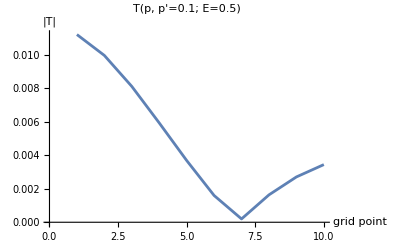

4

5

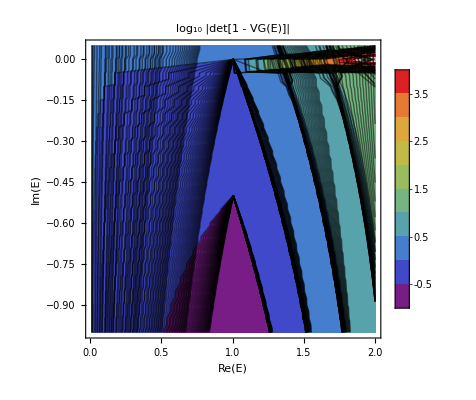

```mathematica
(*---PARAMETERS---*)
M=100;                (* Mass of Nucleon*)
m=0.1*M;               (*Pion mass*)
α=0.8;              (*Depth of Yukawa potential*)
l=0;

nGrid=10;    (*Number of momentum points*)
Λ=10;         (*Momentum cutoff*)
dp=Λ/nGrid;   (*Grid spacing*)
pGrid=N@Table[i*dp,{i,1,nGrid}];


V[r_]:=-α*Exp[-m*r]/r+l(l+1)/(2r^2);

Vell[ℓ_,p_,pp_]:=4π NIntegrate[r ^2 V[r] SphericalBesselJ[ℓ,p r] SphericalBesselJ[ℓ,pp r],{r,0,Infinity},Method->"GlobalAdaptive",MaxRecursion->15]
Print[1]
(*Kernel of the Lippmann-Schwinger equation*)
KernelMatrix[E_]:=Module[{V,G},V=Table[Vell[l,pGrid[[i]],pGrid[[j]]],{i,nGrid},{j,nGrid}];
G=Table[If[i==j,0,(pGrid[[j]]^2 dp)/(E-pGrid[[j]]^2/(M)+I*10^-6)],{i,nGrid},{j,nGrid}];
IdentityMatrix[nGrid]-(1/(2 π^2)) V.G];
Print[2]
(*Solve for T-matrix*)
SolveTMatrix[E_,pIn_]:=Module[{K,rhs,T},K=KernelMatrix[E];
rhs=Table[Vell[l,p,pIn],{p,pGrid}];
T=LinearSolve[K,rhs];
T];
Print[3]
(*Plot T-Matrix or Det[K] on Real Axis (Test)*)
K=KernelMatrix[0.45];
MatrixConditionNumber[K]
ListLinePlot[Abs[SolveTMatrix[0.5+I*10^-4,0.1]],PlotLabel->"T(p, p'=0.1; E=0.5)",AxesLabel->{"grid point","|T|"}]
Print[4]
(*Scan for Det[K] = 0 (checks when its super small)*)
detScan=Table[{ReE,ImE,Log10[Abs[Det[KernelMatrix[ReE+I ImE]]]]},{ReE,0.01,2,0.05},{ImE,-1,0.05,0.05}];
Print[5]
ListContourPlot[detScan,DataRange->{{0.01,2},{-1,0.05}},PlotLegends->Automatic,ColorFunction->"Rainbow",PlotLabel->"log₁₀ |det[1 - VG(E)]|",FrameLabel->{"Re(E)","Im(E)"}]
```